```mathematica
cdf[x_] := Integrate[2Pi(E^(-r/d) + E^(-r/(3d)))/(8 Pi d r) r, {r, 0, x}]
```

```mathematica
cdf[1]
```

1-ⅇ^(-1/d)/4-3/4 ⅇ^(-1/(3 d))

```mathematica
cdf[Infinity]
```

ConditionalExpression[1,Re[d]>0]

```mathematica
cdf[x]
```

1-ⅇ^(-x/d)/4-3/4 ⅇ^(-x/(3 d))

```mathematica
Solve[cdf[x] == u, x, Reals]
```

{{x→ConditionalExpression[3 d Log[Root[1+3 #1^2+(-4+4 u) #1^3&,1]],u<1]}}

```mathematica
Simplify[%, u < 1]
```

{{x→3 d Log[Root[1+3 #1^2+(-4+4 u) #1^3&,1]]}}

```mathematica
FullSimplify[%]
```

{{x→3 d Log[Root[1+3 #1^2+(-4+4 u) #1^3&,1]]}}

```mathematica
N[Solve[1+3x^2+(-4+4u)x^3 == 0/. u-> .99, Reals]]
```

{{x→75.0044}}

```mathematica
s[u_] := N[Solve[1+3x^2+(-4+4u)x^3 == 0, Reals]]
```

```mathematica
s[.9999]
```

{{x→7500.}}

```mathematica
Plot[s[u], {u, 0, 1}]
```

-Graphics-

```mathematica
Integrate[2Pi(E^(-r/d))/(8 Pi d r) r, {r, 0, Infinity}]
```

ConditionalExpression[1/4,Re[d]>0]

```mathematica
Integrate[2Pi(E^(-r/(3d)))/(8 Pi d r) r, {r, 0, Infinity}]
```

ConditionalExpression[3/4,Re[d]>0]

```mathematica
cdf1[x_] :=4 Integrate[2Pi(E^(-r/d))/(8 Pi d r) r, {r, 0,x}]
```

```mathematica
cdf1[x]
```

4 (1/4-ⅇ^(-x/d)/4)

```mathematica
Simplify[%]
```

1-ⅇ^(-x/d)

```mathematica
cdf2[x_] :=  (4/3) Integrate[2Pi(E^(-r/(3d)))/(8 Pi d r) r, {r, 0,x}]
```

```mathematica
cdf2[r]
```

1/3 (3-3 ⅇ^(-r/(3 d)))

```mathematica
Simplify[%]
```

1-ⅇ^(-r/(3 d))

```mathematica
Solve[cdf1[x] == u, x,Reals]
```

{{x→ConditionalExpression[d Log[1/(1-u)],u<1]}}

```mathematica
Solve[cdf2[x] == u,x, Reals]
```

{{x→ConditionalExpression[3 d Log[1/(1-u)],u<1]}}

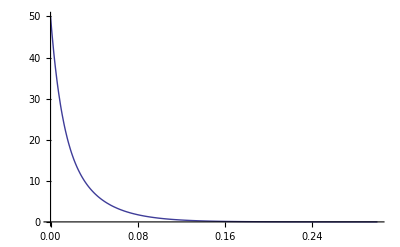

```mathematica
Plot[2Pi r(E^(-r/d) + E^(-r/(3d)))/(8 Pi d r) /. d->.01, {r,0,.3}, PlotRange->All]
```

```mathematica
2Pi(E^(-r/d) + E^(-r/(3d)))/(8 Pi d r) /. {d->.01,r->0.0000000000001}
```

5.×10^14

```mathematica
Limit[E^(-r) / r, r-> 0]
```

∞

```mathematica
Integrate[2Pi(E^(-r/d) + E^(-r/(3d)))/(8 Pi d r) , {r, 0, Infinity}]
```

Integrate::idiv: Integral of ⅇ^-r/d/4\ d\ r + ⅇ^-r/3\ d/4\ d\ r does not converge on {0, ∞}.

∫_0^∞ (ⅇ^(-r/d)+ⅇ^(-r/(3 d)))/(4 d r)ⅆr